```mathematica
ListPointPlot3D[Flatten[Table[Map[{n,#[[1]],#[[2]]}&,FactorInteger[Binomial[2 n, n]]],{n,1,2000}],1], PlotStyle->Opacity[0.5], ColorFunction->"DarkRainbow"]
```

```mathematica
two=Map[{#[[1]],#[[3]]}&,Select[Flatten[Table[Map[{n,#[[1]],#[[2]]}&,FactorInteger[Binomial[2 n, n]]],{n,1,2000}],1],#[[2]]==2&]]
```

{{1,1},{2,1},{3,2},{4,1},{5,2},{6,2},{7,3},{8,1},{9,2},{10,2},{11,3},{12,2},{13,3},{14,3},{15,4},{16,1},{17,2},{18,2},{19,3},{20,2},{21,3},{22,3},{23,4},{24,2},{25,3},{26,3},{27,4},{28,3},{29,4},{30,4},{31,5},{32,1},{33,2},{34,2},{35,3},{36,2},{37,3},{38,3},{39,4},{40,2},{41,3},{42,3},{43,4},{44,3},{45,4},{46,4},{47,5},{48,2},{49,3},{50,3},{51,4},{52,3},{53,4},{54,4},{55,5},{56,3},{57,4},{58,4},{59,5},{60,4},{61,5},{62,5},{63,6},{64,1},{65,2},{66,2},{67,3},{68,2},{69,3},{70,3},{71,4},{72,2},{73,3},{74,3},{75,4},{76,3},{77,4},{78,4},{79,5},{80,2},{81,3},{82,3},{83,4},{84,3},{85,4},{86,4},{87,5},{88,3},{89,4},{90,4},{91,5},{92,4},{93,5},{94,5},{95,6},{96,2},{97,3},{98,3},{99,4},{100,3},{101,4},{102,4},{103,5},{104,3},{105,4},{106,4},{107,5},{108,4},{109,5},{110,5},{111,6},{112,3},{113,4},{114,4},{115,5},{116,4},{117,5},{118,5},{119,6},{120,4},{121,5},{122,5},{123,6},{124,5},{125,6},{126,6},{127,7},{128,1},{129,2},{130,2},{131,3},{132,2},{133,3},{134,3},{135,4},{136,2},{137,3},{138,3},{139,4},{140,3},{141,4},{142,4},{143,5},{144,2},{145,3},{146,3},{147,4},{148,3},{149,4},{150,4},{151,5},{152,3},{153,4},{154,4},{155,5},{156,4},{157,5},{158,5},{159,6},{160,2},{161,3},{162,3},{163,4},{164,3},{165,4},{166,4},{167,5},{168,3},{169,4},{170,4},{171,5},{172,4},{173,5},{174,5},{175,6},{176,3},{177,4},{178,4},{179,5},{180,4},{181,5},{182,5},{183,6},{184,4},{185,5},{186,5},{187,6},{188,5},{189,6},{190,6},{191,7},{192,2},{193,3},{194,3},{195,4},{196,3},{197,4},{198,4},{199,5},{200,3},{201,4},{202,4},{203,5},{204,4},{205,5},{206,5},{207,6},{208,3},{209,4},{210,4},{211,5},{212,4},{213,5},{214,5},{215,6},{216,4},{217,5},{218,5},{219,6},{220,5},{221,6},{222,6},{223,7},{224,3},{225,4},{226,4},{227,5},{228,4},{229,5},{230,5},{231,6},{232,4},{233,5},{234,5},{235,6},{236,5},{237,6},{238,6},{239,7},{240,4},{241,5},{242,5},{243,6},{244,5},{245,6},{246,6},{247,7},{248,5},{249,6},{250,6},{251,7},{252,6},{253,7},{254,7},{255,8},{256,1},{257,2},{258,2},{259,3},{260,2},{261,3},{262,3},{263,4},{264,2},{265,3},{266,3},{267,4},{268,3},{269,4},{270,4},{271,5},{272,2},{273,3},{274,3},{275,4},{276,3},{277,4},{278,4},{279,5},{280,3},{281,4},{282,4},{283,5},{284,4},{285,5},{286,5},{287,6},{288,2},{289,3},{290,3},{291,4},{292,3},{293,4},{294,4},{295,5},{296,3},{297,4},{298,4},{299,5},{300,4},{301,5},{302,5},{303,6},{304,3},{305,4},{306,4},{307,5},{308,4},{309,5},{310,5},{311,6},{312,4},{313,5},{314,5},{315,6},{316,5},{317,6},{318,6},{319,7},{320,2},{321,3},{322,3},{323,4},{324,3},{325,4},{326,4},{327,5},{328,3},{329,4},{330,4},{331,5},{332,4},{333,5},{334,5},{335,6},{336,3},{337,4},{338,4},{339,5},{340,4},{341,5},{342,5},{343,6},{344,4},{345,5},{346,5},{347,6},{348,5},{349,6},{350,6},{351,7},{352,3},{353,4},{354,4},{355,5},{356,4},{357,5},{358,5},{359,6},{360,4},{361,5},{362,5},{363,6},{364,5},{365,6},{366,6},{367,7},{368,4},{369,5},{370,5},{371,6},{372,5},{373,6},{374,6},{375,7},{376,5},{377,6},{378,6},{379,7},{380,6},{381,7},{382,7},{383,8},{384,2},{385,3},{386,3},{387,4},{388,3},{389,4},{390,4},{391,5},{392,3},{393,4},{394,4},{395,5},{396,4},{397,5},{398,5},{399,6},{400,3},{401,4},{402,4},{403,5},{404,4},{405,5},{406,5},{407,6},{408,4},{409,5},{410,5},{411,6},{412,5},{413,6},{414,6},{415,7},{416,3},{417,4},{418,4},{419,5},{420,4},{421,5},{422,5},{423,6},{424,4},{425,5},{426,5},{427,6},{428,5},{429,6},{430,6},{431,7},{432,4},{433,5},{434,5},{435,6},{436,5},{437,6},{438,6},{439,7},{440,5},{441,6},{442,6},{443,7},{444,6},{445,7},{446,7},{447,8},{448,3},{449,4},{450,4},{451,5},{452,4},{453,5},{454,5},{455,6},{456,4},{457,5},{458,5},{459,6},{460,5},{461,6},{462,6},{463,7},{464,4},{465,5},{466,5},{467,6},{468,5},{469,6},{470,6},{471,7},{472,5},{473,6},{474,6},{475,7},{476,6},{477,7},{478,7},{479,8},{480,4},{481,5},{482,5},{483,6},{484,5},{485,6},{486,6},{487,7},{488,5},{489,6},{490,6},{491,7},{492,6},{493,7},{494,7},{495,8},{496,5},{497,6},{498,6},{499,7},{500,6},{501,7},{502,7},{503,8},{504,6},{505,7},{506,7},{507,8},{508,7},{509,8},{510,8},{511,9},{512,1},{513,2},{514,2},{515,3},{516,2},{517,3},{518,3},{519,4},{520,2},{521,3},{522,3},{523,4},{524,3},{525,4},{526,4},{527,5},{528,2},{529,3},{530,3},{531,4},{532,3},{533,4},{534,4},{535,5},{536,3},{537,4},{538,4},{539,5},{540,4},{541,5},{542,5},{543,6},{544,2},{545,3},{546,3},{547,4},{548,3},{549,4},{550,4},{551,5},{552,3},{553,4},{554,4},{555,5},{556,4},{557,5},{558,5},{559,6},{560,3},{561,4},{562,4},{563,5},{564,4},{565,5},{566,5},{567,6},{568,4},{569,5},{570,5},{571,6},{572,5},{573,6},{574,6},{575,7},{576,2},{577,3},{578,3},{579,4},{580,3},{581,4},{582,4},{583,5},{584,3},{585,4},{586,4},{587,5},{588,4},{589,5},{590,5},{591,6},{592,3},{593,4},{594,4},{595,5},{596,4},{597,5},{598,5},{599,6},{600,4},{601,5},{602,5},{603,6},{604,5},{605,6},{606,6},{607,7},{608,3},{609,4},{610,4},{611,5},{612,4},{613,5},{614,5},{615,6},{616,4},{617,5},{618,5},{619,6},{620,5},{621,6},{622,6},{623,7},{624,4},{625,5},{626,5},{627,6},{628,5},{629,6},{630,6},{631,7},{632,5},{633,6},{634,6},{635,7},{636,6},{637,7},{638,7},{639,8},{640,2},{641,3},{642,3},{643,4},{644,3},{645,4},{646,4},{647,5},{648,3},{649,4},{650,4},{651,5},{652,4},{653,5},{654,5},{655,6},{656,3},{657,4},{658,4},{659,5},{660,4},{661,5},{662,5},{663,6},{664,4},{665,5},{666,5},{667,6},{668,5},{669,6},{670,6},{671,7},{672,3},{673,4},{674,4},{675,5},{676,4},{677,5},{678,5},{679,6},{680,4},{681,5},{682,5},{683,6},{684,5},{685,6},{686,6},{687,7},{688,4},{689,5},{690,5},{691,6},{692,5},{693,6},{694,6},{695,7},{696,5},{697,6},{698,6},{699,7},{700,6},{701,7},{702,7},{703,8},{704,3},{705,4},{706,4},{707,5},{708,4},{709,5},{710,5},{711,6},{712,4},{713,5},{714,5},{715,6},{716,5},{717,6},{718,6},{719,7},{720,4},{721,5},{722,5},{723,6},{724,5},{725,6},{726,6},{727,7},{728,5},{729,6},{730,6},{731,7},{732,6},{733,7},{734,7},{735,8},{736,4},{737,5},{738,5},{739,6},{740,5},{741,6},{742,6},{743,7},{744,5},{745,6},{746,6},{747,7},{748,6},{749,7},{750,7},{751,8},{752,5},{753,6},{754,6},{755,7},{756,6},{757,7},{758,7},{759,8},{760,6},{761,7},{762,7},{763,8},{764,7},{765,8},{766,8},{767,9},{768,2},{769,3},{770,3},{771,4},{772,3},{773,4},{774,4},{775,5},{776,3},{777,4},{778,4},{779,5},{780,4},{781,5},{782,5},{783,6},{784,3},{785,4},{786,4},{787,5},{788,4},{789,5},{790,5},{791,6},{792,4},{793,5},{794,5},{795,6},{796,5},{797,6},{798,6},{799,7},{800,3},{801,4},{802,4},{803,5},{804,4},{805,5},{806,5},{807,6},{808,4},{809,5},{810,5},{811,6},{812,5},{813,6},{814,6},{815,7},{816,4},{817,5},{818,5},{819,6},{820,5},{821,6},{822,6},{823,7},{824,5},{825,6},{826,6},{827,7},{828,6},{829,7},{830,7},{831,8},{832,3},{833,4},{834,4},{835,5},{836,4},{837,5},{838,5},{839,6},{840,4},{841,5},{842,5},{843,6},{844,5},{845,6},{846,6},{847,7},{848,4},{849,5},{850,5},{851,6},{852,5},{853,6},{854,6},{855,7},{856,5},{857,6},{858,6},{859,7},{860,6},{861,7},{862,7},{863,8},{864,4},{865,5},{866,5},{867,6},{868,5},{869,6},{870,6},{871,7},{872,5},{873,6},{874,6},{875,7},{876,6},{877,7},{878,7},{879,8},{880,5},{881,6},{882,6},{883,7},{884,6},{885,7},{886,7},{887,8},{888,6},{889,7},{890,7},{891,8},{892,7},{893,8},{894,8},{895,9},{896,3},{897,4},{898,4},{899,5},{900,4},{901,5},{902,5},{903,6},{904,4},{905,5},{906,5},{907,6},{908,5},{909,6},{910,6},{911,7},{912,4},{913,5},{914,5},{915,6},{916,5},{917,6},{918,6},{919,7},{920,5},{921,6},{922,6},{923,7},{924,6},{925,7},{926,7},{927,8},{928,4},{929,5},{930,5},{931,6},{932,5},{933,6},{934,6},{935,7},{936,5},{937,6},{938,6},{939,7},{940,6},{941,7},{942,7},{943,8},{944,5},{945,6},{946,6},{947,7},{948,6},{949,7},{950,7},{951,8},{952,6},{953,7},{954,7},{955,8},{956,7},{957,8},{958,8},{959,9},{960,4},{961,5},{962,5},{963,6},{964,5},{965,6},{966,6},{967,7},{968,5},{969,6},{970,6},{971,7},{972,6},{973,7},{974,7},{975,8},{976,5},{977,6},{978,6},{979,7},{980,6},{981,7},{982,7},{983,8},{984,6},{985,7},{986,7},{987,8},{988,7},{989,8},{990,8},{991,9},{992,5},{993,6},{994,6},{995,7},{996,6},{997,7},{998,7},{999,8},{1000,6},{1001,7},{1002,7},{1003,8},{1004,7},{1005,8},{1006,8},{1007,9},{1008,6},{1009,7},{1010,7},{1011,8},{1012,7},{1013,8},{1014,8},{1015,9},{1016,7},{1017,8},{1018,8},{1019,9},{1020,8},{1021,9},{1022,9},{1023,10},{1024,1},{1025,2},{1026,2},{1027,3},{1028,2},{1029,3},{1030,3},{1031,4},{1032,2},{1033,3},{1034,3},{1035,4},{1036,3},{1037,4},{1038,4},{1039,5},{1040,2},{1041,3},{1042,3},{1043,4},{1044,3},{1045,4},{1046,4},{1047,5},{1048,3},{1049,4},{1050,4},{1051,5},{1052,4},{1053,5},{1054,5},{1055,6},{1056,2},{1057,3},{1058,3},{1059,4},{1060,3},{1061,4},{1062,4},{1063,5},{1064,3},{1065,4},{1066,4},{1067,5},{1068,4},{1069,5},{1070,5},{1071,6},{1072,3},{1073,4},{1074,4},{1075,5},{1076,4},{1077,5},{1078,5},{1079,6},{1080,4},{1081,5},{1082,5},{1083,6},{1084,5},{1085,6},{1086,6},{1087,7},{1088,2},{1089,3},{1090,3},{1091,4},{1092,3},{1093,4},{1094,4},{1095,5},{1096,3},{1097,4},{1098,4},{1099,5},{1100,4},{1101,5},{1102,5},{1103,6},{1104,3},{1105,4},{1106,4},{1107,5},{1108,4},{1109,5},{1110,5},{1111,6},{1112,4},{1113,5},{1114,5},{1115,6},{1116,5},{1117,6},{1118,6},{1119,7},{1120,3},{1121,4},{1122,4},{1123,5},{1124,4},{1125,5},{1126,5},{1127,6},{1128,4},{1129,5},{1130,5},{1131,6},{1132,5},{1133,6},{1134,6},{1135,7},{1136,4},{1137,5},{1138,5},{1139,6},{1140,5},{1141,6},{1142,6},{1143,7},{1144,5},{1145,6},{1146,6},{1147,7},{1148,6},{1149,7},{1150,7},{1151,8},{1152,2},{1153,3},{1154,3},{1155,4},{1156,3},{1157,4},{1158,4},{1159,5},{1160,3},{1161,4},{1162,4},{1163,5},{1164,4},{1165,5},{1166,5},{1167,6},{1168,3},{1169,4},{1170,4},{1171,5},{1172,4},{1173,5},{1174,5},{1175,6},{1176,4},{1177,5},{1178,5},{1179,6},{1180,5},{1181,6},{1182,6},{1183,7},{1184,3},{1185,4},{1186,4},{1187,5},{1188,4},{1189,5},{1190,5},{1191,6},{1192,4},{1193,5},{1194,5},{1195,6},{1196,5},{1197,6},{1198,6},{1199,7},{1200,4},{1201,5},{1202,5},{1203,6},{1204,5},{1205,6},{1206,6},{1207,7},{1208,5},{1209,6},{1210,6},{1211,7},{1212,6},{1213,7},{1214,7},{1215,8},{1216,3},{1217,4},{1218,4},{1219,5},{1220,4},{1221,5},{1222,5},{1223,6},{1224,4},{1225,5},{1226,5},{1227,6},{1228,5},{1229,6},{1230,6},{1231,7},{1232,4},{1233,5},{1234,5},{1235,6},{1236,5},{1237,6},{1238,6},{1239,7},{1240,5},{1241,6},{1242,6},{1243,7},{1244,6},{1245,7},{1246,7},{1247,8},{1248,4},{1249,5},{1250,5},{1251,6},{1252,5},{1253,6},{1254,6},{1255,7},{1256,5},{1257,6},{1258,6},{1259,7},{1260,6},{1261,7},{1262,7},{1263,8},{1264,5},{1265,6},{1266,6},{1267,7},{1268,6},{1269,7},{1270,7},{1271,8},{1272,6},{1273,7},{1274,7},{1275,8},{1276,7},{1277,8},{1278,8},{1279,9},{1280,2},{1281,3},{1282,3},{1283,4},{1284,3},{1285,4},{1286,4},{1287,5},{1288,3},{1289,4},{1290,4},{1291,5},{1292,4},{1293,5},{1294,5},{1295,6},{1296,3},{1297,4},{1298,4},{1299,5},{1300,4},{1301,5},{1302,5},{1303,6},{1304,4},{1305,5},{1306,5},{1307,6},{1308,5},{1309,6},{1310,6},{1311,7},{1312,3},{1313,4},{1314,4},{1315,5},{1316,4},{1317,5},{1318,5},{1319,6},{1320,4},{1321,5},{1322,5},{1323,6},{1324,5},{1325,6},{1326,6},{1327,7},{1328,4},{1329,5},{1330,5},{1331,6},{1332,5},{1333,6},{1334,6},{1335,7},{1336,5},{1337,6},{1338,6},{1339,7},{1340,6},{1341,7},{1342,7},{1343,8},{1344,3},{1345,4},{1346,4},{1347,5},{1348,4},{1349,5},{1350,5},{1351,6},{1352,4},{1353,5},{1354,5},{1355,6},{1356,5},{1357,6},{1358,6},{1359,7},{1360,4},{1361,5},{1362,5},{1363,6},{1364,5},{1365,6},{1366,6},{1367,7},{1368,5},{1369,6},{1370,6},{1371,7},{1372,6},{1373,7},{1374,7},{1375,8},{1376,4},{1377,5},{1378,5},{1379,6},{1380,5},{1381,6},{1382,6},{1383,7},{1384,5},{1385,6},{1386,6},{1387,7},{1388,6},{1389,7},{1390,7},{1391,8},{1392,5},{1393,6},{1394,6},{1395,7},{1396,6},{1397,7},{1398,7},{1399,8},{1400,6},{1401,7},{1402,7},{1403,8},{1404,7},{1405,8},{1406,8},{1407,9},{1408,3},{1409,4},{1410,4},{1411,5},{1412,4},{1413,5},{1414,5},{1415,6},{1416,4},{1417,5},{1418,5},{1419,6},{1420,5},{1421,6},{1422,6},{1423,7},{1424,4},{1425,5},{1426,5},{1427,6},{1428,5},{1429,6},{1430,6},{1431,7},{1432,5},{1433,6},{1434,6},{1435,7},{1436,6},{1437,7},{1438,7},{1439,8},{1440,4},{1441,5},{1442,5},{1443,6},{1444,5},{1445,6},{1446,6},{1447,7},{1448,5},{1449,6},{1450,6},{1451,7},{1452,6},{1453,7},{1454,7},{1455,8},{1456,5},{1457,6},{1458,6},{1459,7},{1460,6},{1461,7},{1462,7},{1463,8},{1464,6},{1465,7},{1466,7},{1467,8},{1468,7},{1469,8},{1470,8},{1471,9},{1472,4},{1473,5},{1474,5},{1475,6},{1476,5},{1477,6},{1478,6},{1479,7},{1480,5},{1481,6},{1482,6},{1483,7},{1484,6},{1485,7},{1486,7},{1487,8},{1488,5},{1489,6},{1490,6},{1491,7},{1492,6},{1493,7},{1494,7},{1495,8},{1496,6},{1497,7},{1498,7},{1499,8},{1500,7},{1501,8},{1502,8},{1503,9},{1504,5},{1505,6},{1506,6},{1507,7},{1508,6},{1509,7},{1510,7},{1511,8},{1512,6},{1513,7},{1514,7},{1515,8},{1516,7},{1517,8},{1518,8},{1519,9},{1520,6},{1521,7},{1522,7},{1523,8},{1524,7},{1525,8},{1526,8},{1527,9},{1528,7},{1529,8},{1530,8},{1531,9},{1532,8},{1533,9},{1534,9},{1535,10},{1536,2},{1537,3},{1538,3},{1539,4},{1540,3},{1541,4},{1542,4},{1543,5},{1544,3},{1545,4},{1546,4},{1547,5},{1548,4},{1549,5},{1550,5},{1551,6},{1552,3},{1553,4},{1554,4},{1555,5},{1556,4},{1557,5},{1558,5},{1559,6},{1560,4},{1561,5},{1562,5},{1563,6},{1564,5},{1565,6},{1566,6},{1567,7},{1568,3},{1569,4},{1570,4},{1571,5},{1572,4},{1573,5},{1574,5},{1575,6},{1576,4},{1577,5},{1578,5},{1579,6},{1580,5},{1581,6},{1582,6},{1583,7},{1584,4},{1585,5},{1586,5},{1587,6},{1588,5},{1589,6},{1590,6},{1591,7},{1592,5},{1593,6},{1594,6},{1595,7},{1596,6},{1597,7},{1598,7},{1599,8},{1600,3},{1601,4},{1602,4},{1603,5},{1604,4},{1605,5},{1606,5},{1607,6},{1608,4},{1609,5},{1610,5},{1611,6},{1612,5},{1613,6},{1614,6},{1615,7},{1616,4},{1617,5},{1618,5},{1619,6},{1620,5},{1621,6},{1622,6},{1623,7},{1624,5},{1625,6},{1626,6},{1627,7},{1628,6},{1629,7},{1630,7},{1631,8},{1632,4},{1633,5},{1634,5},{1635,6},{1636,5},{1637,6},{1638,6},{1639,7},{1640,5},{1641,6},{1642,6},{1643,7},{1644,6},{1645,7},{1646,7},{1647,8},{1648,5},{1649,6},{1650,6},{1651,7},{1652,6},{1653,7},{1654,7},{1655,8},{1656,6},{1657,7},{1658,7},{1659,8},{1660,7},{1661,8},{1662,8},{1663,9},{1664,3},{1665,4},{1666,4},{1667,5},{1668,4},{1669,5},{1670,5},{1671,6},{1672,4},{1673,5},{1674,5},{1675,6},{1676,5},{1677,6},{1678,6},{1679,7},{1680,4},{1681,5},{1682,5},{1683,6},{1684,5},{1685,6},{1686,6},{1687,7},{1688,5},{1689,6},{1690,6},{1691,7},{1692,6},{1693,7},{1694,7},{1695,8},{1696,4},{1697,5},{1698,5},{1699,6},{1700,5},{1701,6},{1702,6},{1703,7},{1704,5},{1705,6},{1706,6},{1707,7},{1708,6},{1709,7},{1710,7},{1711,8},{1712,5},{1713,6},{1714,6},{1715,7},{1716,6},{1717,7},{1718,7},{1719,8},{1720,6},{1721,7},{1722,7},{1723,8},{1724,7},{1725,8},{1726,8},{1727,9},{1728,4},{1729,5},{1730,5},{1731,6},{1732,5},{1733,6},{1734,6},{1735,7},{1736,5},{1737,6},{1738,6},{1739,7},{1740,6},{1741,7},{1742,7},{1743,8},{1744,5},{1745,6},{1746,6},{1747,7},{1748,6},{1749,7},{1750,7},{1751,8},{1752,6},{1753,7},{1754,7},{1755,8},{1756,7},{1757,8},{1758,8},{1759,9},{1760,5},{1761,6},{1762,6},{1763,7},{1764,6},{1765,7},{1766,7},{1767,8},{1768,6},{1769,7},{1770,7},{1771,8},{1772,7},{1773,8},{1774,8},{1775,9},{1776,6},{1777,7},{1778,7},{1779,8},{1780,7},{1781,8},{1782,8},{1783,9},{1784,7},{1785,8},{1786,8},{1787,9},{1788,8},{1789,9},{1790,9},{1791,10},{1792,3},{1793,4},{1794,4},{1795,5},{1796,4},{1797,5},{1798,5},{1799,6},{1800,4},{1801,5},{1802,5},{1803,6},{1804,5},{1805,6},{1806,6},{1807,7},{1808,4},{1809,5},{1810,5},{1811,6},{1812,5},{1813,6},{1814,6},{1815,7},{1816,5},{1817,6},{1818,6},{1819,7},{1820,6},{1821,7},{1822,7},{1823,8},{1824,4},{1825,5},{1826,5},{1827,6},{1828,5},{1829,6},{1830,6},{1831,7},{1832,5},{1833,6},{1834,6},{1835,7},{1836,6},{1837,7},{1838,7},{1839,8},{1840,5},{1841,6},{1842,6},{1843,7},{1844,6},{1845,7},{1846,7},{1847,8},{1848,6},{1849,7},{1850,7},{1851,8},{1852,7},{1853,8},{1854,8},{1855,9},{1856,4},{1857,5},{1858,5},{1859,6},{1860,5},{1861,6},{1862,6},{1863,7},{1864,5},{1865,6},{1866,6},{1867,7},{1868,6},{1869,7},{1870,7},{1871,8},{1872,5},{1873,6},{1874,6},{1875,7},{1876,6},{1877,7},{1878,7},{1879,8},{1880,6},{1881,7},{1882,7},{1883,8},{1884,7},{1885,8},{1886,8},{1887,9},{1888,5},{1889,6},{1890,6},{1891,7},{1892,6},{1893,7},{1894,7},{1895,8},{1896,6},{1897,7},{1898,7},{1899,8},{1900,7},{1901,8},{1902,8},{1903,9},{1904,6},{1905,7},{1906,7},{1907,8},{1908,7},{1909,8},{1910,8},{1911,9},{1912,7},{1913,8},{1914,8},{1915,9},{1916,8},{1917,9},{1918,9},{1919,10},{1920,4},{1921,5},{1922,5},{1923,6},{1924,5},{1925,6},{1926,6},{1927,7},{1928,5},{1929,6},{1930,6},{1931,7},{1932,6},{1933,7},{1934,7},{1935,8},{1936,5},{1937,6},{1938,6},{1939,7},{1940,6},{1941,7},{1942,7},{1943,8},{1944,6},{1945,7},{1946,7},{1947,8},{1948,7},{1949,8},{1950,8},{1951,9},{1952,5},{1953,6},{1954,6},{1955,7},{1956,6},{1957,7},{1958,7},{1959,8},{1960,6},{1961,7},{1962,7},{1963,8},{1964,7},{1965,8},{1966,8},{1967,9},{1968,6},{1969,7},{1970,7},{1971,8},{1972,7},{1973,8},{1974,8},{1975,9},{1976,7},{1977,8},{1978,8},{1979,9},{1980,8},{1981,9},{1982,9},{1983,10},{1984,5},{1985,6},{1986,6},{1987,7},{1988,6},{1989,7},{1990,7},{1991,8},{1992,6},{1993,7},{1994,7},{1995,8},{1996,7},{1997,8},{1998,8},{1999,9},{2000,6}}

```mathematica
Map[#[[1]]&,Select[Flatten[Monitor[Table[Map[{n,#[[1]],#[[2]]}&,FactorInteger[Binomial[2 n, n]]],{n,1,1000}],n],1],#[[3]]==1 && #[[2]]==Prime[1]&]]
```

{1,2,4,8,16,32,64,128,256,512}

```mathematica
FactorBin[n_]:=FactorBin[n]= FactorInteger[Binomial[2 n, n]]
```

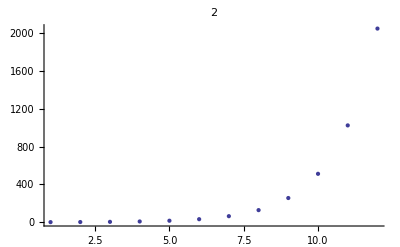

```mathematica
With[
{p = 2, exp=1, range=3000},
ListPlot[Map[#[[1]]&,Select[Flatten[Table[Map[{n,#[[1]],#[[2]]}&,FactorBin[n]],{n,1,range}],1],#[[3]]==exp && #[[2]]==p&]], PlotLabel->p]
]
```